```mathematica
EulerLagrange[L_,q_]:=Block[{lhs,rhs,solution},
lhs = D[D[L,q'[t]],t];
rhs = D[L,q[t]];
solution = Solve[lhs-rhs==0,q''[t]][[1,1,2]];

q''[t]==solution
];
```

# L1

Ref: https://www.youtube.com/watch?time_continue=26&v=U-L23G8lPQ8&feature=emb_logo

```mathematica
L = m h^2 θ1'[t]^2+m A^2 ω^2 Cos[ω t]^2-2 m A ω h θ1'[t] Cos[ω t] Cos[θ1[t]]-2 m g h Cos[θ1[t]]-k θ1[t]^2;
```

```mathematica
EulerLagrange[L_,q_]:=Block[{lhs,rhs},
lhs = D[D[L,q'[t]],t];
rhs = D[L,q[t]];
Solve[lhs-rhs==0,q''[t]]
];
```

```mathematica
EulerLagrange[L,θ1]
```

{{θ1''[t]→(-A h m ω^2 Cos[θ1[t]] Sin[t ω]+g h m Sin[θ1[t]]-k θ1[t])/(h^2 m)}}

```mathematica
g = 9.8;
m = 1;
k = 10;
h = 1;
l = 2;
A =0.5;
ω = 1;
```

```mathematica
Clear[g,m,k,h,l,A,ω]
```

```mathematica
Clear[eventTime];
solutions = NDSolveValue[
{
θ1''[t]==(-A h m ω^2 Cos[θ1[t]] Sin[t ω]+g h m Sin[θ1[t]]-k θ1[t])/(h^2 m),
WhenEvent[Abs[θ1[t]]≥ π/2,eventTime=t;"StopIntegration"],

θ1[0] == 0, θ1'[0]==0
},
{θ1[t]},
{t,0,100}
];
If[Head[eventTime]===Symbol,eventTime = Head[First[solutions]][[1,1,2]]];
```

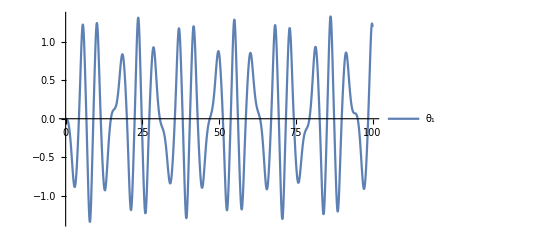

```mathematica
Plot[solutions,{t,0,eventTime},PlotLegends->{"θ_1"},PlotRange->All,GridLines->{{},{-π/2,π/2}}]
```

```mathematica
r1[t_,θ1_]:={A Sin[ω t],0};
r2[t_,θ1_]:={l+A Sin[ω t],0};
r3[t_,θ1_]:={A Sin[ω t]-h Sin[θ1],h Cos[θ1]};
r4[t_,θ1_]:={l+A Sin[ω t]-h Sin[θ1],h Cos[θ1]};

r1[tp_]:=Apply[r1,{t,First[solutions]}/.t->tp];
r2[tp_]:=Apply[r2,{t,First[solutions]}/.t->tp];
r3[tp_]:=Apply[r3,{t,First[solutions]}/.t->tp];
r4[tp_]:=Apply[r4,{t,First[solutions]}/.t->tp];
```

```mathematica
Manipulate[
Graphics[
{
Black,Line[{r1[t],r2[t]}],
Black,Line[{r3[t],r4[t]}],
Orange,Line[{r1[t],r3[t]}],
Orange,Line[{r2[t],r4[t]}],
Brown,Disk[r1[t],0.05],
Brown,Disk[r2[t],0.05],
Blue,Disk[r3[t],0.05],
Blue,Disk[r4[t],0.05]
},
PlotRange->{{-3,6},{-2,2}}
],
{t,0,100}
]
```

#### Para agregar el resorte al diagrama

Ojo: no es la solución con resorte, sólo un diagrama

```mathematica
DropSides[l_List]:=Take[l,{2,-2}];
AppendSides[l_List,left_,right_]:=Join[{left},l,{right}];
OddEven[l_List]:=Flatten[Partition[l,2,2,1,{}],{2}]; (* Source: https://mathematica.stackexchange.com/questions/21468/pretty-way-to-group-elements-at-odd-and-even-positions *)
Spring[{xi_,yi_},{xf_,yf_},div_,width_]:=Block[{xPoints,slope,xyPoints,d,odd,even,normalPointsOdd,normalPointsEven,zigzagPts,springCoords},
xPoints = Range[xi,xf-xi,(xf-xi)/div];
slope = (yf-yi)/(xf-xi);
xyPoints = Table[{x,slope(x-xi)+yi},{x,DropSides[xPoints]}];
{odd,even} = OddEven[xyPoints];
d = width*Normalize[{xf-xi,yf-yi}];
normalPointsOdd = Map[RotationMatrix[π/2].d+#&,odd];
normalPointsEven = Map[RotationMatrix[-π/2].d+#&,even];
zigzagPts = Riffle[normalPointsOdd,normalPointsEven];
springCoords = AppendSides[zigzagPts,{xi,yi},{xf,yf}];

Line[springCoords]
];
```

```mathematica
Manipulate[
Graphics[
{
Black,Line[{r1[t],r2[t]}],
Black,Line[{r3[t],r4[t]}],
Orange,Line[{r1[t],r3[t]}],
Orange,Line[{r2[t],r4[t]}],
Red,Spring[r1[t],r4[t],15,0.07],
Brown,Disk[r1[t],0.05],
Brown,Disk[r2[t],0.05],
Blue,Disk[r3[t],0.05],
Blue,Disk[r4[t],0.05]
},
PlotRange->{{-1,3},{-2,2}}
],
{t,0,100}
]
```